```mathematica
Quadrature point understanding
```

```mathematica
1)Legendre polynomials
```

```mathematica
P0=1;
P1=x;
P2=(1/2)(3x^2-1);
P3=(1/2)(5x^3-3x);
P4=(1/8)(35x^4-30x^2+3);
P5=(1/8)(63x^4-70x^3+15x);
P6=(1/16)(231x^6-315x^4+105x^2-5);
P7=(1/16)(429x^7-693x^5+315x^3-35x);
```

{-0.5+a-c/2+(3 e)/8,0.234+b-(3 d)/2,1.+(3 c)/2-(15 e)/4,-0.234+(5 d)/2,-1+(35 e)/8}

{{a→0.366667,b→-0.0936,c→-0.0952381,d→0.0936,e→0.228571}}

{0.5-0.234 x-1. x^2+0.234 x^3+1. x^4}

0.733333

0.733333

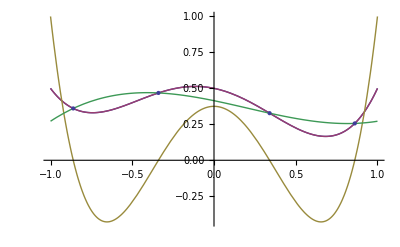

```mathematica
Clear[a,b,c,d,e]
f=x^4-10x^3+x^2-x;
f=(x+0.234)(x-1)(x+1)(1x)+0.5;
La=a P0+b P1+c P2+d P3+e P4;
fa=CoefficientList[La-f,x]
eq={};
For[i=1,i≤First[Dimensions[fa]],i=i+1,eq=Append[eq,Extract[fa,i]==0]];
ss=Solve[eq,{a,b,c,d,e}]

af=Expand[(La)/.ss]
f1=f/.x->-0.33998104358485626;
f2=f/.x->0.33998104358485626;
f3=f/.x->0.8611363115940526;
f4=f/.x->-0.8611363115940526;
x1=-0.33998104358485626;
x2=0.33998104358485626;
x3=0.8611363115940526;
x4=-0.8611363115940526;
w1=0.652145;
w2=0.652145;
w3=0.347855;
w4=0.347855;
w1 f1+w2 f2 +w3 f3+w4 f4
NIntegrate[f,{x,-1,1}]

l1=(x-x2)(x-x3)(x-x4)/((x1-x2)(x1-x3)(x1-x4));
l2=(x-x1)(x-x3)(x-x4)/((x2-x1)(x2-x3)(x2-x4));
l3=(x-x1)(x-x2)(x-x4)/((x3-x1)(x3-x2)(x3-x4));
l4=(x-x1)(x-x2)(x-x3)/((x4-x1)(x4-x2)(x4-x3));
Show[Plot[{f,af,P4,l1 f1+l2 f2+l3 f3+l4 f4},{x,-1,1}],ListPlot[{{x1,f1},{x2,f2},{x3,f3},{x4,f4}}]]
```

```mathematica
N[Reduce[P4==0]]
```

x==-0.339981||x==0.339981||x==-0.861136||x==0.861136

```mathematica
La/.x->x1
```

a-0.339981 b-0.326619 c+0.411728 d+5.55112×10^-17 e

```mathematica
Expand[l1 f1+l2 f2+l3 f3+l4 f4]
NIntegrate[Expand[l1 f1+l2 f2+l3 f3+l4 f4],{x,-1,1}]
```

0.414286-0.234 x-0.142857 x^2+0.234 x^3

0.733333

```mathematica
3 term Reccurance Relation ship between orthogonal polynomials;
```

```mathematica
Error in polynomial approximation
1) Using Taylor seires;
       2)Orthogonal polynomials
            3)the best approximtion possible
```

```mathematica
Quick learning: Given a nice symmteric PDF in 1D - explore revolving a continuous polynomial, can we get the product formula , the corresponding orthogonal polynomials and the respective quadrature rules. Try to use these polynomial approximations and quadratures for solving
1) The FPK equations
     2) The eg in PF tutorial paper.
```

```mathematica
NN[x_,mu_,s_]:=(1/Sqrt[2Pi s^2])Exp[-(x-mu)^2/s^2];
PDx=0.5 NN[x,1,1]+0.5NN[x,-1,1];
PDy=0.9 NN[y,2,1]+0.1NN[y,-1,1];
Plot3D[PDx PDy,{x,-10,10},{y,-10,10},Mesh->0.1,PlotRange->{{-10,10},{-10,10},{0,0.1}}]
```

Mesh::ilevels: 0.1 is not a valid mesh specification.

-Graphics3D-

```mathematica
(*3 Term recurrence rlation ship*)
notes.. the orthogonal polynomials are formed from solving moment equations.
Subscript[c, k]=∫w(x)x^mⅆx
Assume 
Subscript[P, n](x)=x^n+Subscript[a, n,n-1] x^(n-1)... Subscript[a, n,0]
Construct the a's in Pn  by saying that it is orthogonal to all other x^m m<n
∫w(x)x^m Subscript[P, n](x)ⅆx=0
```

```mathematica
Subscript[P, n]=(x-Subscript[β, n])Subscript[P, n-1]-Subscript[γ, n] Subscript[P, n-2]
Subscript[P, 1]
```

x P_n

```mathematica
Integrate[P3 P3,{x,-1,1}]
```

2/7